# Energy Calculations

## Constants

```mathematica
Needs["Developer`"]
lengthVOX=.45737;(*Units nm*)
kB=1.380649*^-23; (* boltzmanns constant [J/K] *)
ϵ0=8.854*^-12; (*vacuum permittivity: ϵ0=8.854*^-12 [C^2/(J m)]*)
m2nm=10^9;(*m to nm*)
J2meV=6.642*^18*1000;(*J to meV*)
debye2Cm=3.3356*^-30;
Ang2mVol=1^3/((10^10)^3);(*Å^3 to m^3*)
eV2J=1.602*^-19;(*eV to J*)
e2C=1.602*^-19;(*e to C*)
totCON1=(m2nm)^6*J2meV;(*Front load conversion to nm and meV*)
totCON2=(m2nm)^2*J2meV;(*Front load conversion to nm and meV*)
totCON3=m2nm*J2meV;(*Front load conversion to nm and meV*)
```

## How to determine voxel meaning

### SWNT geometry properties as applicable to energy

```mathematica
(*SWNT chiral indixing selection*)
m=6;
n=5;
index={m,n};
a0=0.2461;(*Two carbon atoms distance in nm*)
CpolVOL=1.76;(*Carbon Polarizabily for Carbon Å^3, https://cccbdb.nist.gov/pollistx.asp*)

SWNTdiam=(a0 √(m^2+m*n+n^2))/π;(*SWNT diameter (nm)*)
SWNTrad=SWNTdiam/2;

aTRANs=(a0 √(3*(m^2+m*n+n^2)))/(GCD[m,n]*If[IntegerQ[(m-n)/(3*GCD[m,n])]==True,3,1]);(*translational period of unit cell in nm*)

ac=(4*(m^2+m*n+n^2))/(GCD[m,n]*If[IntegerQ[(m-n)/(3*GCD[m,n])]==True,3,1]);(*atoms per unit cell*)

acPERnm=ac/aTRANs;(*atoms/nm*)
acPERvox=(acPERnm*lengthVOX)/2;(*atoms/voxel, divided by 2 because 2 voxels per length*)
SWNTpolVOL=acPERvox*CpolVOL;

SWNTionPOT=5;(*eV from Table 1 in 10.1016/j.physe.2013.07.004, not sure why 5eV was choosen from the table*) 

Print["Chirility",{m,n},", ","Radius ",SWNTrad,"nm"]
```

Chirility{6,5}, Radius 0.373639nm

### aDEX geometry properties as applicable to energy

```mathematica
aDEX150=150000;(*aDEX MW (g/mol)*)
ringMW=206;(*MW of a single ring of aDEX (g/mol)*)
NOaDEXrings=N[aDEX150/ringMW];(*Number of aDEX rings/aDEX globular*)
aDEXvoxNO=9435;(*Number of voxels aDEX take*)
ringPERvox=NOaDEXrings/aDEXvoxNO(*Rings/voxel*)
```

0.077176

## Variables

```mathematica
Chs=2.4*10^-3;(* hard sphere coefficient in units of meV*nm^12, taken from From https://pubs.acs.org/doi/full/10.1021/nn4058402 "A" term*)
T=298;(*Temperature K*)
ϵ=30; (*relative permittivity Can alter in a range of 10-80*)(*For hydrogels they range from 30-50*)
SDSperVOX=0.537;(*Average number of SDS molecules/SWNT length of voxel dimension*)

(*Dipole Moments for SWNT, aDEX, MBA, ASR*)
ddMOpre={29.5709*SDSperVOX+0.0732/10,ringPERvox*5.557,.89072683/2,11.2932};(*Results from AMS*)
ddMO=ddMOpre*debye2Cm(*Debye to Cm*)

(*Polarizability volume for SWNT, aDEX, MBA, ASR*)
polVOLpre={36.9956*SDSperVOX+104.568/2,ringPERvox*30.878,21.82/2,6.9285};(*Results from AMS*)
polVOL=polVOLpre*Ang2mVol;(*Å^3 to m^3*)

(*Ionization potential for SWNT, aDEX, MBA, ASR*)
ionPOTpre={9.735*SDSperVOX+5,ringPERvox*9.268,10.133/2,10.149};(*Results from AMS*)
ionPOT=ionPOTpre*eV2J;(*eV to J*)

(*Charge for SWNT, aDEX, MBA, ASR*)
CHARpre={-1*SDSperVOX,0,0,-1};
char=CHARpre*e2C(*e to C*)

SWNT={ddMO[[1]],polVOL[[1]],ionPOT[[1]] ,char[[1]]} ;
aDEX={ddMO[[2]],polVOL[[2]],ionPOT[[2]] ,char[[2]]}; 
MBA={ddMO[[3]],polVOL[[3]],ionPOT[[3]],char[[3]]};
PS={ddMO[[4]],polVOL[[4]],ionPOT[[4]] ,char[[4]]} ;
{{"Energy Type","SWNT","aDEX","MBA","ASR"},
{"Dipole Moment",ddMOpre[[1]],ddMOpre[[2]],ddMOpre[[3]],ddMOpre[[4]]},
{"Polarizability Volume",polVOLpre[[1]],polVOLpre[[2]],polVOLpre[[3]],polVOLpre[[4]]},
{"Ionization Potential",ionPOTpre[[1]],ionPOTpre[[2]],ionPOTpre[[3]],ionPOTpre[[4]]},
{"Charge",CHARpre[[1]],CHARpre[[2]],CHARpre[[3]],CHARpre[[4]]}}//MatrixForm
```

{5.29923×10^-29,1.43053×10^-30,1.48555×10^-30,3.76696×10^-29}

{-8.60274×10^-20,0.,0.,-1.602×10^-19}

(Energy Type | SWNT | aDEX | MBA | ASR
Dipole Moment | 15.8869 | 0.428867 | 0.445363 | 11.2932
Polarizability Volume | 72.1506 | 2.38304 | 10.91 | 6.9285
Ionization Potential | 10.2277 | 0.715267 | 5.0665 | 10.149
Charge | -0.537 | 0 | 0 | -1)

## Energy Functions

### Hard Sphere

28.6417 meV

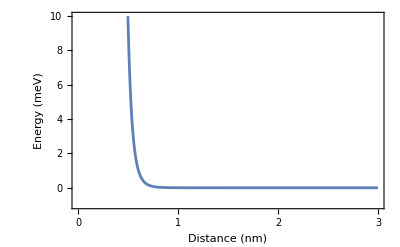

```mathematica
Uhs[d_]:=Chs/d^12;(*Dimensional Analysis: (meV*nm^12)/nm^12*)

Uhs[lengthVOX]"meV"(*Energy at smalest distance*)
Plot[Uhs[d],{d,0,3},PlotRange->{-1,10},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Energy (meV)",None},{"Distance (nm)",None}},FrameTicks->All]
```

### Dipole-Dipole

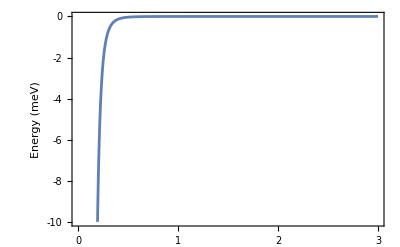

```mathematica
(*SWNT1, POS 1 Different component, Temp*)

piϵϵ0=4*π*ϵ*ϵ0;
uddCON=(2*totCON1)/((piϵϵ0)^2*3*kB);
Udd[d_,μ1_,μ2_,T_]:=-(μ1^2*μ2^2)/(T*d^6)*uddCON;(*meter to nm ((10^9 nm)^6)/m^6, J to meV=6.642*^18*1000*)
(*Dimensional analysis: ((Cm)^2*(Cm)^2)/((C^2/(J m))^2*J/K*K)1/nm^6*((10^9 nm)^6)/m^6(6.642*^18eV)/J(1000meV)/ev=meV*)

Plot[Udd[d,SWNT[[1]],aDEX[[1]],T],{d,0,3},PlotRange->{-10,0},Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"Energy (meV)",None},{None,"Distance (nm)"}},FrameTicks->All]
```

### Dipole-Induced Dipole

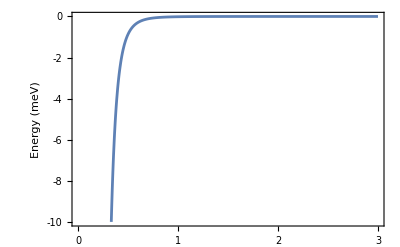

```mathematica
(*SWNT1, POS 1 Different, component SWNT2, POS 2 Different component*)

piϵϵ0=4*π*ϵ*ϵ0;
uindCON=totCON1/piϵϵ0;
Uind[d_,μ1_,μ2_,PV1_,PV2_]:=-μ1^2/1(PV2)uindCON/d^6-μ2^2/1(PV1)uindCON/d^6;
(*meter to nm ((10^9 nm)^6)/m^6, J to meV=6.642*^18*1000*)
(*Dimensional analysis: ((Cm)^2 m^3)/(C^2/(J m))1/nm^6*((10^9 nm)^6)/m^6(6.642*^18eV)/J(1000meV)/ev=meV*)

Plot[Uind[d,SWNT[[1]],aDEX[[1]],SWNT[[2]],aDEX[[2]]],{d,0,3},PlotRange->{-10,0},Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"Energy (meV)",None},{None,"Distance (nm)"}},FrameTicks->All]
```

### London Dispersion Attraction

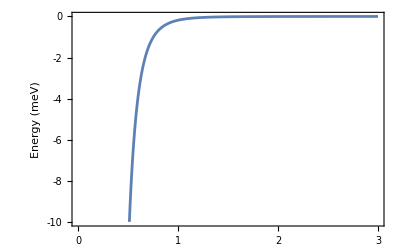

```mathematica
udispCON=(3*totCON1)/2;
Udisp[d_,I1_,I2_,PV1_,PV2_]:=-((I1*I2)/(I1+I2))(PV1*PV2)udispCON/d^6;
(*meter to nm ((10^9 nm)^6)/m^6, J to meV=6.642*^18*1000*)
(*Dimensional analysis: (J*J)/J(m^3 m^3)/nm^6*((10^9 nm)^6)/m^6(6.642*^18eV)/J(1000meV)/ev=meV*)

Plot[Udisp[d,SWNT[[3]],aDEX[[3]],SWNT[[2]],aDEX[[2]]],{d,0,3},PlotRange->{-10,0},Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"Energy (meV)",None},{None,"Distance (nm)"}},FrameTicks->All]
```

### Ion-Dipole

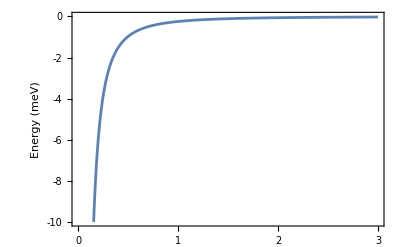

```mathematica
piϵϵ0=4*π*ϵ*ϵ0;
uiondipCON=totCON2/piϵϵ0;
Uiondip[d_,μ1_,μ2_,q1_,q2_]:=((q1*μ2)/d^2+(q2*μ1)/d^2)*uiondipCON;
(*meter to nm ((10^9 nm)^2)/m^6, J to meV=6.642*^18*1000*)
(*Dimensional analysis: 1/(C^2/Jm)(Cm*C)/nm^2*((10^9 nm)^2)/m^2(6.642*^18eV)/J(1000meV)/ev=meV*)

Plot[Uiondip[d,SWNT[[1]],aDEX[[1]],SWNT[[4]],aDEX[[4]]],{d,0,3},PlotRange->{-10,0},Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"Energy (meV)",None},{None,"Distance (nm)"}},FrameTicks->All]
```

### Coulombs Interactions

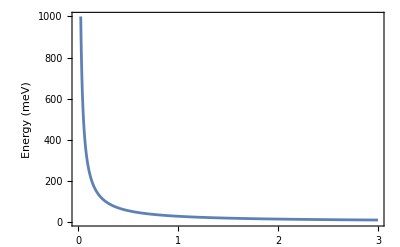

```mathematica
piϵϵ0=4*π*ϵ*ϵ0;
ucolCON=totCON3/piϵϵ0;
Ucol[d_,q1_,q2_]:=(q1*q2)/d*ucolCON;

Plot[Ucol[d,SWNT[[4]],PS[[4]]],{d,0,3},PlotRange->{0,1000},Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"Energy (meV)",None},{None,"Distance (nm)"}},FrameTicks->All]
```

### Sum of Energies Functions

#### aDEX

```mathematica
SWNTaDEX[d_]:=Module[{sumENERGY},

sumENERGY={_,_,_,_,_,_};

sumENERGY[[1]]=Uhs[d];
sumENERGY[[2]]=Udd[d,SWNT[[1]],aDEX[[1]],T];
sumENERGY[[3]]=Uind[d,SWNT[[1]],aDEX[[1]],SWNT[[2]],aDEX[[2]]];
sumENERGY[[4]]=Udisp[d,SWNT[[3]],aDEX[[3]],SWNT[[2]],aDEX[[2]]];
sumENERGY[[5]]=Uiondip[d,SWNT[[1]],aDEX[[1]],SWNT[[4]],aDEX[[4]]];
sumENERGY[[6]]=Ucol[d,SWNT[[4]],aDEX[[4]]];

sumENERGY
];
```

#### MBA

```mathematica
SWNTMBA[d_]:=Module[{sumENERGY},

sumENERGY={_,_,_,_,_,_};

sumENERGY[[1]]=Uhs[d];
sumENERGY[[2]]=Udd[d,SWNT[[1]],MBA[[1]],T];
sumENERGY[[3]]=Uind[d,SWNT[[1]],MBA[[1]],SWNT[[2]],MBA[[2]]];
sumENERGY[[4]]=Udisp[d,SWNT[[3]],MBA[[3]],SWNT[[2]],MBA[[2]]];
sumENERGY[[5]]=Uiondip[d,SWNT[[1]],MBA[[1]],SWNT[[4]],MBA[[4]]];
sumENERGY[[6]]=Ucol[d,SWNT[[4]],MBA[[4]]];

sumENERGY
];
```

#### ASR

```mathematica
SWNTPS[d_]:=

Module[{sumENERGY},

sumENERGY={_,_,_,_,_,_};

sumENERGY[[1]]=Uhs[d];
sumENERGY[[2]]=Udd[d,SWNT[[1]],PS[[1]],T];
sumENERGY[[3]]=Uind[d,SWNT[[1]],PS[[1]],SWNT[[2]],PS[[2]]];
sumENERGY[[4]]=Udisp[d,SWNT[[3]],PS[[3]],SWNT[[2]],PS[[2]]];
sumENERGY[[5]]=Uiondip[d,SWNT[[1]],PS[[1]],SWNT[[4]],PS[[4]]];
sumENERGY[[6]]=Ucol[d,SWNT[[4]],PS[[4]]];

sumENERGY
]
```

## Distance to Energy Conversion

### Sum of Energies for CNT gel

#### aDEX

```mathematica
aDEXdistALL=Import["\\Hydrogel Data\\Gel Opt Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\aDEX\\aDEXdistALL.mx"];
aDEXtotLENGTHs=aDEXdistALL*lengthVOX;
Clear[aDEXdistALL]
```

```mathematica
aDEXtotENERGY=ToPackedArray[Table[ConstantArray[0.,6],{i,1,Length[aDEXtotLENGTHs]}]];

SetSharedVariable[aDEXtotENERGY];

AbsoluteTiming[
ParallelDo[
aDEXtotENERGY[[j]]=

Total[Table[SWNTaDEX[aDEXtotLENGTHs[[j,i]]],{i,1,Length[aDEXtotLENGTHs[[j]]]}]];

,{j,1,Length[aDEXtotENERGY]},ProgressReporting->True];]
```

{219.03,Null}

```mathematica
Export["\\Modeling 3D Gel\\Gel Optimization Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\Energies\\aDEXtotENERGY.mx",aDEXtotENERGY];
```

#### MBA

```mathematica
Clear[aDEXtotENERGY]
MBAdistALL=Import["\\Hydrogel Data\\Gel Opt Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\MBA\\MBAdistALL.mx"];
MBAtotLENGTHs=MBAdistALL*lengthVOX;
Clear[MBAdistALL]
```

```mathematica
MBAtotENERGY=ToPackedArray[Table[ConstantArray[0.,6],{i,1,Length[MBAtotLENGTHs]}]];

SetSharedVariable[MBAtotENERGY];

AbsoluteTiming[
ParallelDo[
MBAtotENERGY[[j]]=

Total[Table[SWNTMBA[MBAtotLENGTHs[[j,i]]],{i,1,Length[MBAtotLENGTHs[[j]]]}]];

,{j,1,Length[MBAtotENERGY]},ProgressReporting->True];]
```

{63.1089,Null}

```mathematica
Export["\\Modeling 3D Gel\\Gel Optimization Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\Energies\\MBAtotENERGY.mx",MBAtotENERGY];
```

#### ASR

```mathematica
Clear[MBAtotENERGY]
ASRdistALL=Import["\\Hydrogel Data\\Gel Opt Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\ASR\\ASRdistALL.mx"];
ASRtotLENGTHs=ASRdistALL*lengthVOX;
Clear[ASRdistALL]
```

```mathematica
ASRtotENERGY=ToPackedArray[Table[ConstantArray[0.,6],{i,1,Length[ASRtotLENGTHs]}]];

SetSharedVariable[ASRtotENERGY];

AbsoluteTiming[
ParallelDo[
ASRtotENERGY[[j]]=

ToPackedArray[Total[Table[SWNTPS[ASRtotLENGTHs[[j,i]]],{i,1,Length[ASRtotLENGTHs[[j]]]}]]];

,{j,1,Length[ASRtotENERGY]},ProgressReporting->True];]
```

{3.34735,Null}

```mathematica
Export["\\Modeling 3D Gel\\Gel Optimization Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\Energies\\ASRtotENERGY.mx",ASRtotENERGY];
```

#### Sum of energies

```mathematica
aDEXtotENERGY=Import["\\Modeling 3D Gel\\Gel Optimization Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\Energies\\aDEXtotENERGY.mx" ];
```

```mathematica
MBAtotENERGY=Import["\\Modeling 3D Gel\\Gel Optimization Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\Energies\\MBAtotENERGY.mx"];
```

```mathematica
ASRtotENERGY=Import["\\Modeling 3D Gel\\Gel Optimization Voxel=APS\\CNT and Gel\\CNT Placed Inside Gel\\GEL 80-80-1.0\\Gel 1\\CNT Placement 1\\Point Distances\\Energies\\ASRtotENERGY.mx"];
```

```mathematica
{{"aDEX"},{{"HS","DD","IND-D","Lond-Disp","Ion-D","Col-Int"},Total[aDEXtotENERGY]}//MatrixForm}//MatrixForm

{{"MBA"},{{"HS","DD","IND-D","Lond-Disp","Ion-D","Col-Int"},Total[MBAtotENERGY]}//MatrixForm}//MatrixForm

{{"ASR"},{{"HS","DD","IND-D","Lond-Disp","Ion-D","Col-Int"},Total[ASRtotENERGY]}//MatrixForm}//MatrixForm

{{"HS","DD","IND-D","Lond-Disp","Ion-D","Col-Int"},
Total[aDEXtotENERGY]+Total[MBAtotENERGY]+Total[ASRtotENERGY]}//MatrixForm

Total[Flatten[aDEXtotENERGY]]+Total[Flatten[MBAtotENERGY]]+Total[Flatten[ASRtotENERGY]]
```

({aDEX}
(HS | DD | IND-D | Lond-Disp | Ion-D | Col-Int
0.00121602 | -0.0573677 | -1.40652 | -18.9591 | -55081.7 | 0.))

({MBA}
(HS | DD | IND-D | Lond-Disp | Ion-D | Col-Int
395.47 | -1.65719 | -169.642 | -11783.7 | -13387.6 | 0.))

({ASR}
(HS | DD | IND-D | Lond-Disp | Ion-D | Col-Int
2.26434×10^-8 | -0.0105149 | -0.00662284 | -0.111028 | -1016.21 | 14392.3))

(HS | DD | IND-D | Lond-Disp | Ion-D | Col-Int
395.471 | -1.72507 | -171.055 | -11802.7 | -69485.6 | 14392.3)

-66673.3